```mathematica
Clear[ω,Q,α,τ]
Q[α_] := 1/(3-α); (*Güte*)
τ:=1; (*R·C in s*)

A[ω_,α_] :=α/(1+ⅈ*ω*τ/Q[α]+(ⅈ*ω*τ)^2)
Α = {1,1.268, 1.586, 2.234};
```

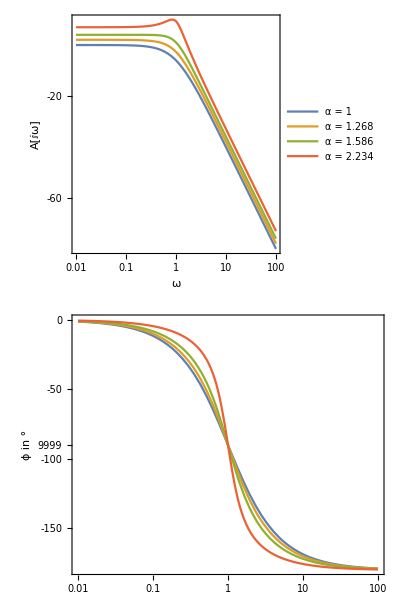

```mathematica
BodePlot[{A[ω,Α[[1]]],A[ω,Α[[2]]],A[ω,Α[[3]]], A[ω,Α[[4]]]}, {ω,0.01,100},
ImageSize->Medium, FrameLabel->{{"ω", "A[ⅈω] in dB"},{" ", "ϕ in °"}},
PlotLegends->{"α = " Text[Α[[1]]], "α = " Text[Α[[2]]], "α = " Text[Α[[3]]], "α = " Text[Α[[4]]]}]
```

```mathematica
AbsA[ω_] = Abs[{A[ω,Α[[1]]],A[ω,Α[[2]]],A[ω,Α[[3]]], A[ω,Α[[4]]]}];
AbsAdB[ω_]:=N[20*Log[10,AbsA[ω]]];
```

```mathematica
Ares = AbsAdB[1/τ]
```

{-6.0206,-2.70857,0.997075,9.29709}

```mathematica
Azero = AbsAdB[0]
```

{0.,2.06239,4.00606,6.98166}

```mathematica
DeltaA = Ares-Azero
```

{-6.0206,-4.77096,-3.00899,2.31542}